```mathematica
xbar[ka_,x_]:=(ka*x)/(1+(ka*x))
```

```mathematica
xrange=Table[Power[10,-ii],{ii,0,15,0.01}];
```

```mathematica
ka10pow3=Table[{Log[x],xbar[10^3,x]},{x,xrange}];
ka10pow6=Table[{Log[x],xbar[10^6,x]},{x,xrange}];
ka10pow9=Table[{Log[x],xbar[10^9,x]},{x,xrange}];
```

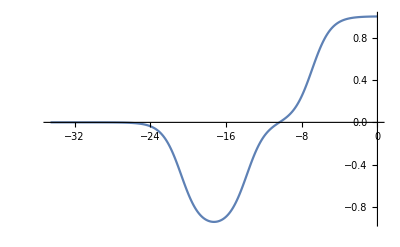

```mathematica
(*Ka 10^3 + Ka 10^6 - Ka 10^9*)
ListLinePlot[ka10pow3+ka10pow6-ka10pow9]
```